```mathematica
Clear["Global`*"]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::slwcon]]
ParallelEvaluate[Off[NIntegrate::izero]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

```mathematica
ϵ = 1.*8065.5 (*100*);
alpha=N[400/π] (*(0.05 ϵ)/π*)(*10/3.14*);
ω0 =8000 ;
wc =53  (*0.1 ϵ*);
Γ =ϵ/10(* N[ω0^2/wc]; *)(* Width of distribution *)
Temp = 300;
kB = 0.695;
```

806.55

```mathematica
ρ00i = 0.5;
ρ01i = 0.5;
ρ10i = 0.5;
ρ11i= 0.5;
```

```mathematica
β =1/(kB Temp)(*0.95/ϵ *)(**)
```

0.00479616

```mathematica
J[ω_,α_]:= (α Γ ω0^2 ω)/((ω0^2 - ω^2)^2 + Γ^2 ω^2) (**)

Jod[ω_, α_] :=  (α ω wc)/(ω^2+wc^2)
```

```mathematica
w0List = {200, 400, 600}
```

{200,400,600}

```mathematica
Plot
```

Plot

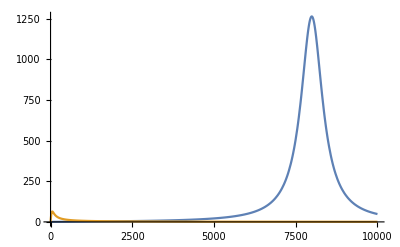

```mathematica
Plot[{J[ω, alpha],Jod[ω, alpha]}, {ω,0, 10000},PlotRange->All]
```

```mathematica
(*S1:= -4 NIntegrate[J[ω]/ω^2 Coth[ω/(2 kB Temp)], {ω, 0, 10wc}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->30 ]*)
S[t_]:=- NIntegrate[J[ω,alpha]/ω^2 Coth[(ω β)/2] (1-Cos[ω t]), {ω, 0, ∞}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40,AccuracyGoal->8 ]
```

```mathematica
rho10[t_] := ρ10i Exp[S[t]] Exp[ⅈ ϵ t]
 rho01[t_] := ρ01i Exp[S[t]] Exp[-ⅈ ϵ t]
```

```mathematica
rho10[0.001]
```

-0.100286+0.467031 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

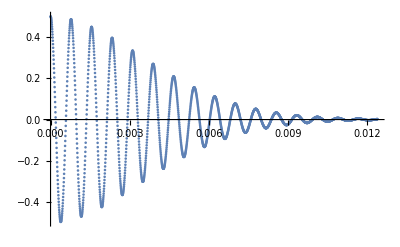

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

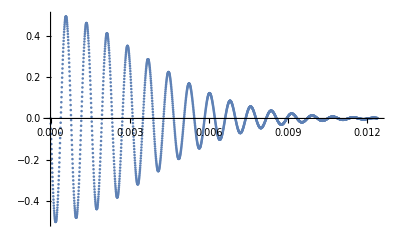

```mathematica
t0 = 0; tf= 100/ϵ; di =(tf-t0)/2000;
tlist = N[Range[t0,tf, di]];
ListPlot[Transpose@{tlist, Re@rho01[tlist]}, PlotRange->All]
ListPlot[Transpose@{tlist, Im@rho01[tlist]}, PlotRange->All]
```

```mathematica
data=Transpose@{tlist, Re@rho01[tlist]};
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Directory[]
```

/home/henry

```mathematica
Export["Work/phd-work/vibronic-TLS/DATA/Exactdata.dat",data]
```

Work/phd-work/vibronic-TLS/DATA/Exactdata.dat

Absorption Spectra

```mathematica
(*ω0 = 100; Γ=10000;*)
```

```mathematica
J[ω_, α_]:= (α Γ ω0^2 ω)/((ω0^2 - ω^2)^2 + Γ^2 ω^2)
```

```mathematica
J[0, 1]
```

0

```mathematica
μ = 1;
(*α=100; β =10;*)
```

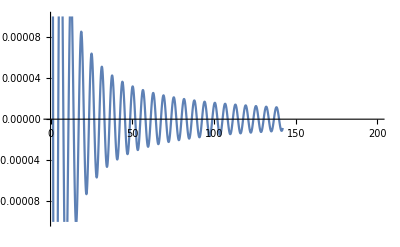

```mathematica
Plot[Re[J[ω, alpha]/ω^2 (Cos[ω]Coth[(β ω)/2]+ⅈ Sin[ω])],  {ω,0,300}, PlotRange->{{0, 200}, {-0.0001, 0.0001}}]
```

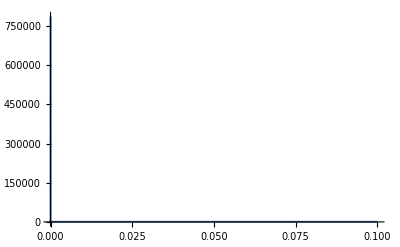

```mathematica
Plot[J[ω, alpha]/ω^2, {ω,0,0.1}, PlotRange->All]
```

```mathematica
Assuming[Ω>0&&τ∈Reals,Integrate[(a ω Exp[-ω/Ω])/ω^2 (1-Cos[ω τ]+ⅈ Sin[ω τ]),{ω,0, ∞}]]
```

1/2 a (2 ⅈ ArcTan[τ Ω]+Log[1+τ^2 Ω^2])

```mathematica
(*Φ[τ_] := NIntegrate[(ω Exp[-ω/10])/ω^2 (Cos[ω τ]Coth[(β ω)/2]-ⅈ Sin[ω τ]),{ω,0, ∞} ,Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]*)
```

```mathematica
Φ[τ_] := NIntegrate[J[ω, alpha]/ω^2 ((1-Cos[ω τ])Coth[(β ω)/2]+ⅈ Sin[ω τ]),{ω,0, ∞} ,Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]
```

```mathematica
DiscretePlot[{Re[Exp[-Φ[t]]],Im[Exp[-Φ[t]]]},{t,0,1,0.001},PlotRange->All,Joined->True,Filling->None]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368543+0.00252046 ⅈ and 3.76884×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368785+0.00252047 ⅈ and 4.06012×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368944+0.00252047 ⅈ and 4.19727×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

```mathematica
phi=Interpolation[ParallelTable[{τ,Φ[τ]},{τ,0,0.2,0.0001}]]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368487+0.00252046 ⅈ and 3.81471×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368503+0.00252046 ⅈ and 3.72849×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368511+0.00252047 ⅈ and 3.89777×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

InterpolatingFunction[{{0., 0.2}}, <>]

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368543+0.00252046 ⅈ and 3.76884×10^-8 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0368543+0.00252046 ⅈ and 3.76884×10^-8 for the integral and error estimates.

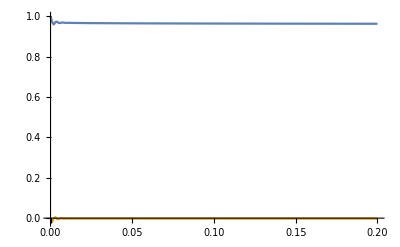

```mathematica
DiscretePlot[{Re[Exp[-Φ[t]]],Im[Exp[-Φ[t]]]},{t,0,0.2,0.001},PlotRange->All,Joined->True,Filling->None]
```

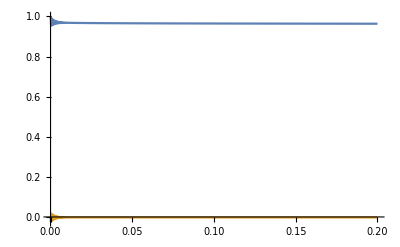

```mathematica
Plot[{Re[Exp[-phi[t]]],Im[Exp[-phi[t]]]},{t,0,0.2},PlotRange->All]
```

```mathematica
shift=NIntegrate[J[ω, alpha]/ω,{ω,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {7257.97}. NIntegrate obtained 205.289 and 51.5661 for the integral and error estimates.

205.289

```mathematica
S[x_]:=NIntegrate[Exp[-phi[τ] ]Exp[ⅈ(x+shift) τ],{τ, 0, ∞},Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]
```

```mathematica
(*S[ω_, ϵ_]:=NIntegrate[Exp[-Φ[τ] ]Exp[ⅈ(ω-ϵ) τ],{τ, 0, ∞},Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]*)
```

```mathematica
(*S[ω_, ϵ_]:=NIntegrate[Exp[Φ[τ]-1 ]Exp[i (ω-ϵ) τ],{τ, 0, ∞},Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

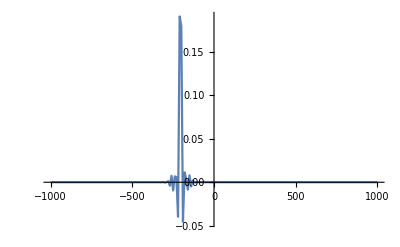

```mathematica
DiscretePlot[Re[S[x]],{x,-1000,1000,10},PlotRange->All,Joined->True,Filling->None]
```